### Explicit Examples

```mathematica
α = ({{α1}, {α2}, {α3}, {α4}});
β1=({{β11}, {β12}, {β13}, {β14}});
β2=({{β21}, {β22}, {β23}, {β24}});
β3=({{β31}, {β32}, {β33}, {β34}});
β4=({{β41}, {β42}, {β43}, {β44}});
A0=({{0, 0, 0, 0}, {A021, 0, 0, 0}, {A031, A032, 0, 0}, {A041, A042, A043, 0}}); (* A0=({{A011, A012, A013, A014}, {A021, A022, A023, A024}, {A031, A032, A033, A034}, {A041, A042, A043, A044}}); *)
A1=({{0, 0, 0, 0}, {A121, 0, 0, 0}, {A131, A132, 0, 0}, {A141, A142, A143, 0}}); (* Subscript[A, 1]=({{A111, A112, A113, A114}, {A121, A122, A123, A124}, {A131, A132, A113, A134}, {A141, A142, A143, A144}}); *)
B0=({{0, 0, 0, 0}, {B021, 0, 0, 0}, {B031, B032, 0, 0}, {B041, B042, B043, 0}}); (* Subscript[B, 0]=({{B011, B012, B013, B014}, {B021, B022, B023, B024}, {B031, B032, B033, B034}, {B041, B042, B043, B044}}); *)
B1=({{0, 0, 0, 0}, {B121, 0, 0, 0}, {B131, B132, 0, 0}, {B141, B142, B143, 0}}); (* Subscript[B, 1]=({{B111, B112, B113, B114}, {B121, B122, B123, B124}, {B131, B132, B133, B134}, {B141, B142, B143, B144}}); *)
e = ({{1}, {1}, {1}, {1}});
constraints[A011_,A012_,A013_,A014_,A021_,A022_,A023_,A024_,A031_,A032_,A033_,A034_,A041_,A042_,A043_,A044_,
A111_,A112_,A113_,A114_,A121_,A122_,A123_,A124_,A131_,A132_,A133_,A134_,A141_,A142_,A143_,A144_,
B011_,B012_,B013_,B014_,B021_,B022_,B023_,B024_,B031_,B032_,B033_,B034_,B041_,B042_,B043_,B044_,
B111_,B112_,B113_,B114_,B121_,B122_,B123_,B124_,B131_,B132_,B133_,B134_,B141_,B142_,B143_,B144_,
α1_,α2_,α3_,α4_,β11_,β12_,β13_,β14_,β21_,β22_,β23_,β24_,β31_,β32_,β33_,β34_,β41_,β42_,β43_,β44_]:={α1+α2+α3+α4==1,β11+β12+β13+β14==1,β21+β22+β23+β24==0,β31+β32+β33+β34==0,β41+β42+β43+β44==0,B121 β12+B131 β13+B132 β13+B141 β14+B142 β14+B143 β14==0,B121 β22+B131 β23+B132 β23+B141 β24+B142 β24+B143 β24==1,B121 β32+B131 β33+B132 β33+B141 β34+B142 β34+B143 β34==0,B121 β42+B131 β43+B132 β43+B141 β44+B142 β44+B143 β44==0}
higherConstraints[A011_,A012_,A013_,A014_,A021_,A022_,A023_,A024_,A031_,A032_,A033_,A034_,A041_,A042_,A043_,A044_,
A111_,A112_,A113_,A114_,A121_,A122_,A123_,A124_,A131_,A132_,A133_,A134_,A141_,A142_,A143_,A144_,
B011_,B012_,B013_,B014_,B021_,B022_,B023_,B024_,B031_,B032_,B033_,B034_,B041_,B042_,B043_,B044_,
B111_,B112_,B113_,B114_,B121_,B122_,B123_,B124_,B131_,B132_,B133_,B134_,B141_,B142_,B143_,B144_,
α1_,α2_,α3_,α4_,β11_,β12_,β13_,β14_,β21_,β22_,β23_,β24_,β31_,β32_,β33_,β34_,β41_,β42_,β43_,β44_] := {α1+α2+α3+α4==1,β11+β12+β13+β14==1,β21+β22+β23+β24==0,β31+β32+β33+β34==0,β41+β42+β43+β44==0,B121 β12+B131 β13+B132 β13+B141 β14+B142 β14+B143 β14==0,B121 β22+B131 β23+B132 β23+B141 β24+B142 β24+B143 β24==1,B121 β32+B131 β33+B132 β33+B141 β34+B142 β34+B143 β34==0,B121 β42+B131 β43+B132 β43+B141 β44+B142 β44+B143 β44==0,A021 α2+A031 α3+A032 α3+A041 α4+A042 α4+A043 α4==1/2,B021 α2+B031 α3+B032 α3+B041 α4+B042 α4+B043 α4==1,B021^2 α2+(B031+B032)^2 α3+(B041+B042+B043)^2 α4==3/2,A121 β12+A131 β13+A132 β13+A141 β14+A142 β14+A143 β14==1,A121 β22+A131 β23+A132 β23+A141 β24+A142 β24+A143 β24==0,A121 β32+A131 β33+A132 β33+A141 β34+A142 β34+A143 β34==-1,A121 β42+A131 β43+A132 β43+A141 β44+A142 β44+A143 β44==0,B121^2 β12+(B131+B132)^2 β13+(B141+B142+B143)^2 β14==1,B121^2 β22+(B131+B132)^2 β23+(B141+B142+B143)^2 β24==0,B121^2 β32+(B131+B132)^2 β33+(B141+B142+B143)^2 β34==-1,B121^2 β42+(B131+B132)^2 β43+(B141+B142+B143)^2 β44==2,B121 B132 β13+(B121 B142+(B131+B132) B143) β14==0,B121 B132 β23+(B121 B142+(B131+B132) B143) β24==0,B121 B132 β33+(B121 B142+(B131+B132) B143) β34==0,B121 B132 β43+(B121 B142+(B131+B132) B143) β44==1,1/2 (A132 B021 β13+(A142 B021+A143 (B031+B032)) β14)+1/3 (A132 B021 β33+(A142 B021+A143 (B031+B032)) β34)==0}
Get["stableRegionsEq.mx"]
zmin = -14;
zmax = 1;
wmin = -3;
wmax = 3;
ymin = -4;
ymax = 4;
```

jOpt.9060366.comet-31-11

{0.276228,4.5862,-4.30997,1.22993,-2.43472,1.70479,0.106551,-0.638964,1.37066,-1.29158,2.29728,-0.00568785,-0.000654628,4.42684,-4.79757,2.09394,-1.90427,0.915353,0.3264,0.317006,-0.785171,1.03444,-1.07156,-1.12745,0.119088,-0.98932,0.723226,1.14701,-2.13788,2.28824,0.348343,0.5013,-2.03943,2.3168,-0.11375,-0.163617,3.13788,-2.28823,-0.348342,-0.5013,-1.33147,2.301,-2.69976,1.73024}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

4.43356

-Graphics3D-

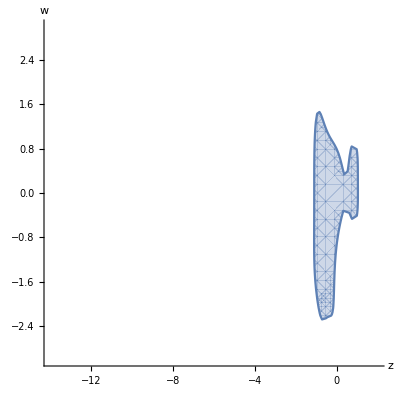

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]

Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.27622806801019867,4.586202890639971,-4.309973448641022,1.2299293752045668,-2.4347181364421893,1.7047881977185728,0.10655070833041062,-0.6389638953648463,1.3706649220569544,-1.2915849319369694,2.297275977168464,-0.005687848699002706,-0.0006546284196073803,4.426835784035641,-4.797568711084061,2.0939418168476536,-1.9042652754658125,0.9153533897264267,0.3264000229399668,0.31700572552656686,-0.785170879408249,1.0344401014901266,-1.0715630950688786,-1.127445298172489,0.11908781218934049,-0.9893204472617865,0.7232261921888061,1.1470062615057315,-2.1378790800639296,2.2882365383846444,0.34834344291878194,0.5012995986328709,-2.039430437882726,2.316796523212927,-0.113750293105376,-0.16361677963262253,3.1378767508479988,-2.2882340016755838,-0.34834219853695775,-0.5012999406632084,-1.331473079412136,2.3009952920518524,-2.6997616118429115,1.7302397112012218}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

jOpt.9060360.comet-31-08

{0.113592,-1.87262,2.18932,4.04538,-3.18606,-0.359327,0.415612,-0.111059,0.526662,0.939229,0.0676601,-0.00688879,0.0370441,-0.119006,1.67425,-0.185748,2.36463,-1.21132,-0.644738,1.97315,-0.780631,2.52129,-2.01897,-1.26622,-2.97345,3.50845,0.714864,-0.249859,0.00328217,-0.420406,0.414783,1.00234,0.908349,-1.82182,0.267426,0.646043,0.996722,0.420395,-0.414782,-1.00233,-3.31635,4.66406,1.01083,-2.35854}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

7.56742

-Graphics3D-

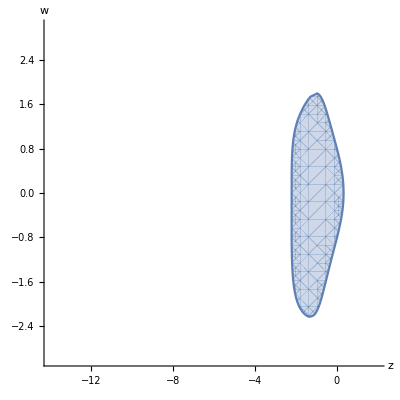

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]

Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.11359173574602198,-1.8726188497738716,2.1893226380027433,4.04538211129286,-3.186055511573977,-0.35932689260369494,0.415612342445249,-0.1110594188833126,0.5266624286881068,0.9392292987868001,0.06766006416678959,-0.006888786867557688,0.03704412962778706,-0.1190056489108845,1.674247915189363,-0.18574846644834642,2.3646304565137934,-1.2113176380742405,-0.6447383851480322,1.9731472737350755,-0.7806311731466471,2.521293594078323,-2.018965139893835,-1.2662216904498353,-2.9734546821348347,3.508449547918439,0.7148642802409588,-0.2498593408958851,0.0032821678697222342,-0.42040581843831204,0.4147825068315771,1.0023402207949332,0.9083489129514718,-1.8218177418086905,0.2674260263302545,0.6460425809201351,0.9967222637388331,0.42039505802361254,-0.4147819128631324,-1.002333805126359,-3.316346279539399,4.6640557111600724,1.0108268791449389,-2.3585368289788735}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

#### jOpt.9060354.comet-31-03

{0.459851,-0.587472,1.08745,1.67402,3.38612,-4.56014,0.0769662,0.612877,-0.535879,-0.75983,1.87521,-0.115385,0.0954955,-2.83863,4.36426,-3.75363,2.01017,2.73616,0.277413,-1.55956,2.84653,0.694645,-2.05218,0.405775,-0.0343296,0.427199,0.668949,-0.0618188,-2.37822,2.52873,0.0478029,0.801692,-2.66741,2.90307,-0.0132452,-0.22242,3.37824,-2.52874,-0.0478007,-0.801694,3.4104,-4.97805,1.28332,0.284328}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

8.08372

-Graphics3D-

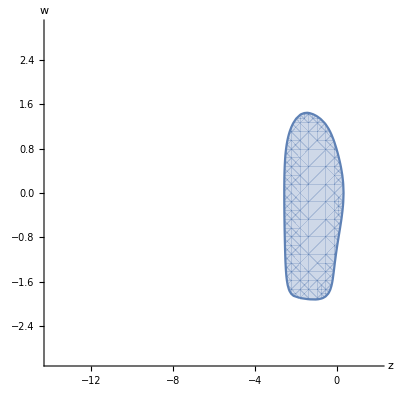

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.4598507989145295,-0.5874722529095457,1.0874523009877761,1.6740180369113327,3.3861187915865316,-4.560136584915967,0.0769661713372989,0.6128766267877671,-0.5358790742594493,-0.7598303239819446,1.8752149209608755,-0.1153851161004008,0.095495472856663,-2.838627009249854,4.364263645801639,-3.7536335754710146,2.010172956663475,2.73616488649968,0.27741301922174927,-1.559563068738087,2.8465318409940132,0.6946445040926884,-2.0521848916994876,0.4057749219004618,-0.034329573865120304,0.42719887479789503,0.6689490354792932,-0.06181875495185937,-2.3782237543713403,2.52872848506248,0.04780289782510631,0.8016919726660879,-2.667407130445926,2.903074391328017,-0.013245157023787995,-0.222420053092094,3.378237864446732,-2.5287437978681746,-0.047800739378405836,-0.8016936747934388,3.410402382890044,-4.978045917474247,1.2833157805436533,0.2843277273430467}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

{0.271691,1.19081,-0.915126,2.73937,-0.135021,-1.60435,0.661458,0.542379,0.130379,0.449243,0.185604,0.365153,2.04159,-1.50666,0.307664,-2.08015,0.429651,0.519801,0.813301,-0.122735,2.17453,-0.0170053,-0.428404,-0.0208899,0.680884,0.414619,-0.666634,0.57113,-0.06691,0.0131019,0.190912,0.862896,-0.361838,1.2189,-0.155269,-0.701794,1.06691,-0.0131019,-0.190912,-0.862896,0.260208,-1.4191,0.67295,0.485945}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

3.88357

-Graphics3D-

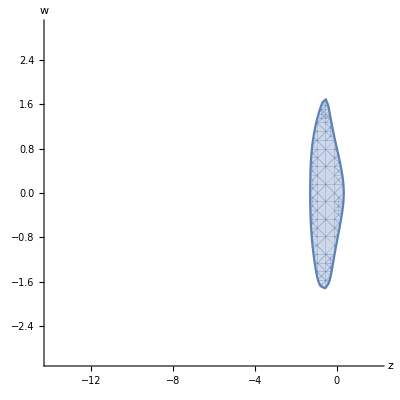

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.2716906476825717,1.1908065280428046,-0.9151255910877345,2.739373156387843,-0.13502090576766732,-1.6043522506201764,0.6614584293988452,0.5423792900461517,0.13037867601048042,0.44924273773616974,0.1856040236610545,0.36515323860277543,2.0415913194211632,-1.5066639342778108,0.30766391605085064,-2.0801530889416355,0.42965095267821984,0.5198013653347396,0.8133009503931496,-0.12273477820227562,2.1745255525453606,-0.01700528545732794,-0.4284035813663027,-0.020889894093037892,0.680884477854352,0.4146193160981084,-0.6666338470095158,0.5711300530538287,-0.06690997454007595,0.013101856874633297,0.19091206249421588,0.8628960551977115,-0.3618382639762742,1.2189014032022751,-0.15526896244250887,-0.7017941770271886,1.0669099745061565,-0.013101856868012327,-0.190912062498961,-0.8628960551667523,0.26020764788551676,-1.419102634194007,0.672950184703745,0.4859448017093759}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

{0.443262,-0.508317,1.35483,-0.304544,0.753375,0.551169,0.347762,0.349263,-0.000223123,0.571721,0.432726,-0.00444673,0.0131775,1.27842,0.00505596,0.746864,-0.207028,0.180048,0.589752,-0.826722,2.70958,0.735737,0.580137,1.09086,0.171093,0.292416,1.08222,-0.545733,0.713669,0.977855,-2.0761,1.38458,-1.52681,1.11904,1.22425,-0.816479,0.286331,-0.977854,2.0761,-1.38458,1.23571,-1.53209,-0.36319,0.659562}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

5.39817

-Graphics3D-

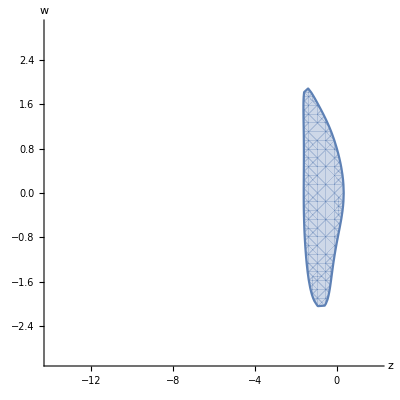

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.44326246072761005,-0.5083170189146073,1.3548293166580976,-0.3045438962010959,0.7533747659788016,0.5511690437002547,0.3477622901649995,0.3492626825461487,-0.00022312263887158757,0.5717207704736362,0.43272595864581437,-0.00444672911945001,0.013177506412276377,1.2784227062987412,0.00505596215112309,0.7468635745523436,-0.2070278661418468,0.18004778561133625,0.5897516820833032,-0.8267216844645245,2.7095822813047943,0.7357368604274369,0.580137105097844,1.0908644255379174,0.17109271300203208,0.29241646845589914,1.082223367434815,-0.5457326889632168,0.7136685253354528,0.9778545308220756,-2.076102826937312,1.3845793939026954,-1.5268111320545628,1.1190405547997022,1.2242505996191198,-0.8164794505558035,0.2863308872923232,-0.9778543769209889,2.076103663661657,-1.384579941480774,1.2357122452297948,-1.5320851151401884,-0.3631902670127944,0.6595619745096987}]

higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

#### jOpt.9086904.comet-31-16

{0.440381,0.42717,0.518418,0.0444978,-1.39519,2.35069,0.603804,0.863925,0.0771224,0.0619527,1.2483,-0.310251,0.205741,0.766536,0.17441,1.0922,1.18375,-1.10387,0.777048,0.934773,-0.461244,-3.03997,0.384897,1.04608,1.10549,-1.02662,-0.569296,1.49042,-0.118133,0.204484,0.629602,0.284046,-0.418079,1.12803,-0.489231,-0.220718,1.11813,-0.204484,-0.629602,-0.284046,-0.698052,2.02724,-1.78338,0.454188}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

3.94622

-Graphics3D-

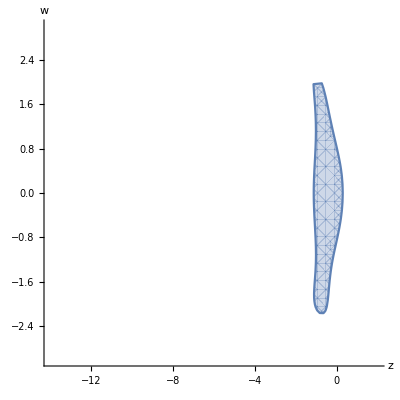

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.44038132509127764,0.4271702135443247,0.5184175371267047,0.04449777003886763,-1.395189654960713,2.3506918849218454,0.603803580787104,0.863924995763391,0.07712236942311482,0.0619527400605521,1.2482984753155033,-0.31025127415257914,0.20574089546422583,0.7665362364572428,0.17441001943330092,1.0921979316386548,1.1837471552294254,-1.1038660447307256,0.7770480474636434,0.9347729995313103,-0.4612444186243542,-3.0399672778126883,0.38489708536670936,1.046076399277951,1.1054935567170578,-1.0266220600481526,-0.5692959625880218,1.4904244364180252,-0.11813266052310618,0.20448436450440308,0.6296019970980663,0.28404629758497324,-0.4180789830613543,1.128027477117982,-0.4892308799249051,-0.22071760233439272,1.118132689416763,-0.20448429658634118,-0.629602092585839,-0.2840462890819767,-0.6980520851709697,2.0272443459027056,-1.7833798255135254,0.45418755120198223}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

#### jOpt.9086908.comet-31-17

{0.0521257,0.805218,-0.0683894,1.6535,-1.6209,0.967401,0.92014,0.719227,0.26398,1.07456,0.0724616,-0.147017,0.0937385,-0.084246,0.605316,0.825557,1.11349,-0.477741,0.959235,0.0398731,-0.432246,-0.637351,1.55946,0.892176,-0.695358,1.38353,-0.440987,0.752815,0.00476745,-0.252247,0.916013,0.331469,-0.0878165,1.28445,-0.878676,-0.317953,0.995243,0.252241,-0.916014,-0.331468,0.134897,-1.81365,0.591855,1.0869}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

5.24872

-Graphics3D-

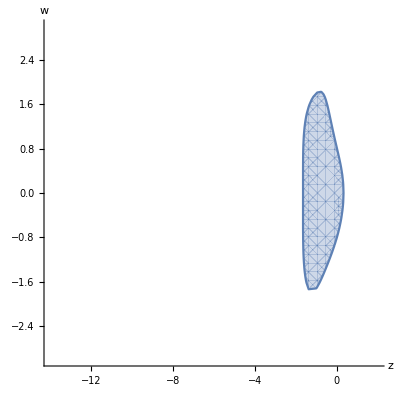

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.05212568303327841,0.8052178895610803,-0.06838935370271365,1.6534959223920642,-1.6208976867105278,0.9674008045499721,0.9201403245822867,0.7192265547286826,0.2639804499226525,1.0745552433162542,0.0724616464802808,-0.14701694891110775,0.09373852416088385,-0.08424603300805063,0.6053156750020944,0.8255570889572127,1.1134909948714675,-0.47774054882357186,0.9592353426310576,0.03987312944046746,-0.43224598489691896,-0.6373514950004593,1.5594607318292584,0.8921761235504029,-0.6953582742036462,1.3835290932307878,-0.44098719779356027,0.7528154612340382,0.004767445797699841,-0.25224664464984387,0.9160131535006943,0.3314693648173897,-0.08781648482690155,1.284446710985852,-0.8786757632909833,-0.317952926316347,0.9952428553620289,0.252241371872735,-0.9160139482945343,-0.3314676103616336,0.1348969999530905,-1.8136544369370289,0.5918549281996678,1.0869023104541973}]

higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```